Figure 2:

```mathematica
gridCells=GridGraph[{10,10}];
```

```mathematica
vs=VertexList[gridCells];
```

```mathematica
cellCoordinates2D=Flatten[Table[{x,y},{x,0,1,1/9},{y,0,1,1/9}],1];
```

The following line takes a while to run:

```mathematica
geneExp2DG3Ts=Table[NMaximize[{(Sum[(2-((1-c1[i])^2+(c2[i])^2+(c3[i])^2))((2-(Mean@((2-((1-#[[1]])^2+(#[[2]])^2+(#[[3]])^2))&/@({c1[#],c2[#],c3[#]}&/@Complement[VertexList@NeighborhoodGraph[gridCells,i,j],{i}]))))),{i,vs}])
(Sum[(2-((c1[i])^2+(1-c2[i])^2+(c3[i])^2))((2-(Mean@((2-((#[[1]])^2+(1-#[[2]])^2+(#[[3]])^2))&/@({c1[#],c2[#],c3[#]}&/@Complement[VertexList@NeighborhoodGraph[gridCells,i,j],{i}]))))),{i,vs}])(Sum[(2-((c1[i])^2+(c2[i])^2+(1-c3[i])^2))((2-(Mean@((2-((#[[1]])^2+(#[[2]])^2+(1-#[[3]])^2))&/@({c1[#],c2[#],c3[#]}&/@Complement[VertexList@NeighborhoodGraph[gridCells,i,j],{i}]))))),{i,vs}])
,(And@@(1≥#>0&/@Flatten[Table[{c1[i],c2[i],c3[i]},{i,vs}]]))&&And@@(Total[#]==1&/@(Table[{c1[i],c2[i],c3[i]},{i,vs}]))},Flatten[Table[{c1[i],c2[i],c3[i]},{i,vs}]]],{j,{1,2,3,4,6,10,15}}];
```

```mathematica
geneExp2DG3Ts2=Join[Chop[Table[{c1[i],c2[i],c3[i]},{i,vs}]/.#,10^-2],{{1,0,0},{0,1,0},{0,0,1}}]&/@geneExp2DG3Ts[[;;,2]];
```

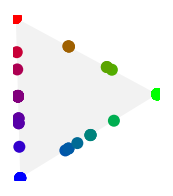
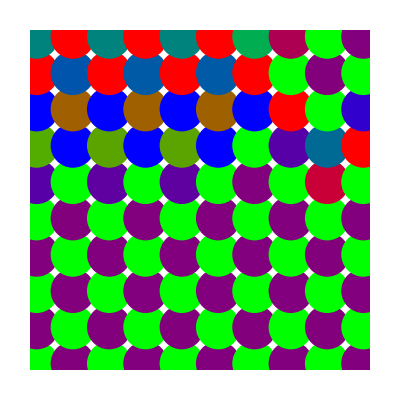
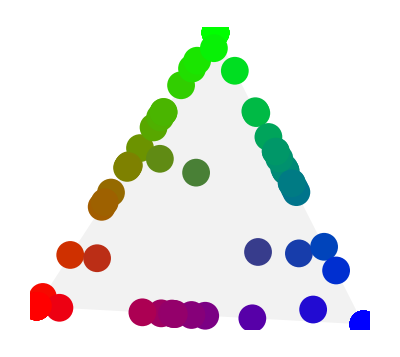
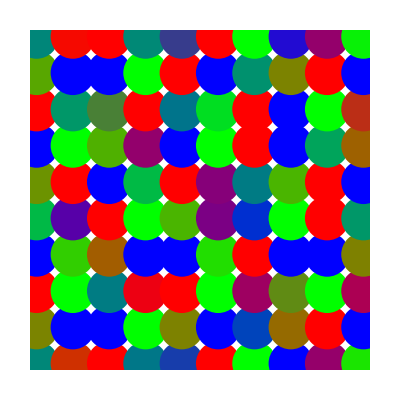
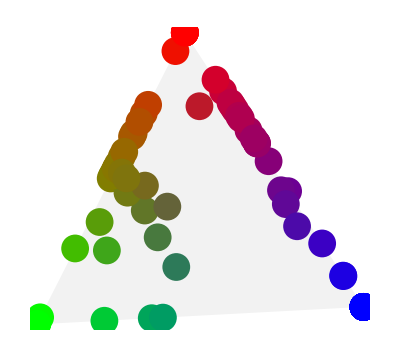
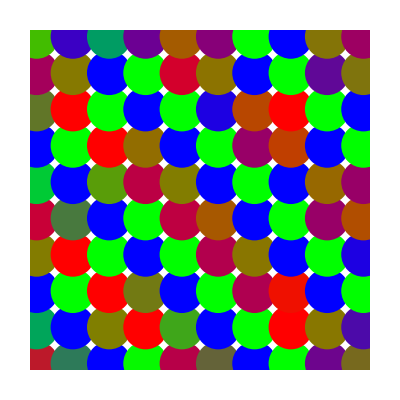
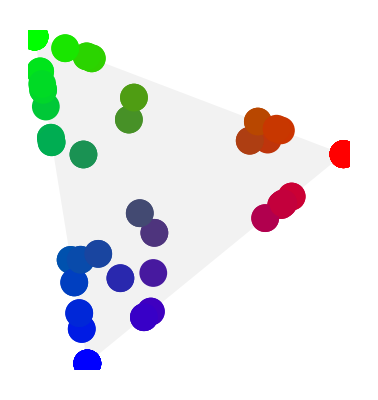
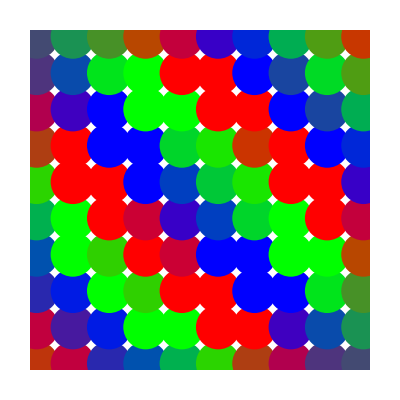

```mathematica
{Show[Graphics[{Opacity[0.05],Simplex[PrincipalComponents[#][[-3;;,;;2]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({PrincipalComponents[#][[;;-4,;;2]],#[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->True,ImageSize->Small]],Graphics[Flatten[{PointSize[.08],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({cellCoordinates2D,#[[;;-4]]}ᵀ)}]]}&/@geneExp2DG3Ts2
```

```mathematica
geneExp2DG3Ts=Table[NMaximize[{(Sum[(2-((1-c1[i])^2+(c2[i])^2+(c3[i])^2))/2((1-(Mean@(((2-((1-#[[1]])^2+(#[[2]])^2+(#[[3]])^2))/2)&/@({c1[#],c2[#],c3[#]}&/@Complement[VertexList@NeighborhoodGraph[gridCells,i,j],{i}]))))),{i,vs}])
(Sum[((2-((c1[i])^2+(1-c2[i])^2+(c3[i])^2))/2)((1-(Mean@((2-((#[[1]])^2+(1-#[[2]])^2+(#[[3]])^2))/2&/@({c1[#],c2[#],c3[#]}&/@Complement[VertexList@NeighborhoodGraph[gridCells,i,j],{i}]))))),{i,vs}])(Sum[(2-((c1[i])^2+(c2[i])^2+(1-c3[i])^2))/2((1-(Mean@((2-((#[[1]])^2+(#[[2]])^2+(1-#[[3]])^2))/2&/@({c1[#],c2[#],c3[#]}&/@Complement[VertexList@NeighborhoodGraph[gridCells,i,j],{i}]))))),{i,vs}])
,(And@@(1≥#>0&/@Flatten[Table[{c1[i],c2[i],c3[i]},{i,vs}]]))&&And@@(Total[#]==1&/@(Table[{c1[i],c2[i],c3[i]},{i,vs}]))},Flatten[Table[{c1[i],c2[i],c3[i]},{i,vs}]]],{j,1,15,1}];
```

```mathematica
geneExp2DG3Ts2=Join[Chop[Table[{c1[i],c2[i],c3[i]},{i,vs}]/.#,10^-2],{{1,0,0},{0,1,0},{0,0,1}}]&/@geneExp2DG3Ts[[;;,2]];
```

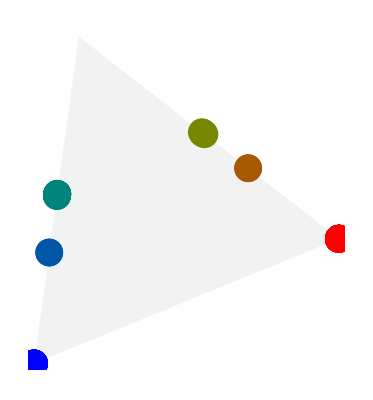
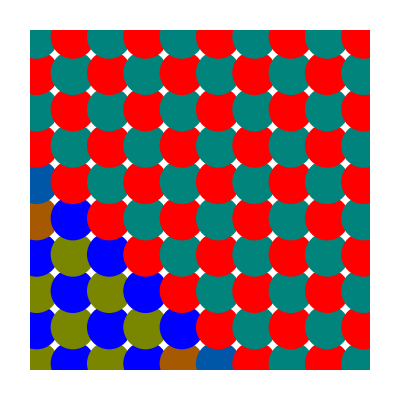
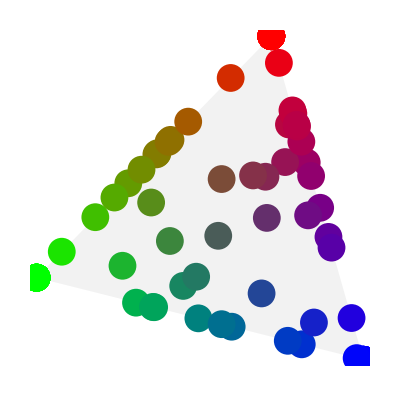
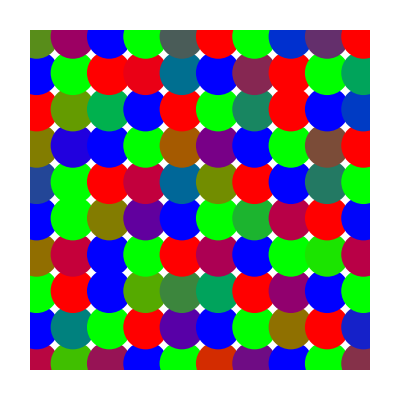
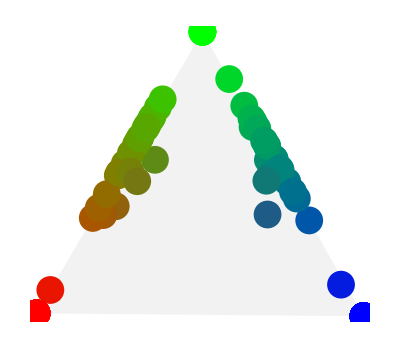
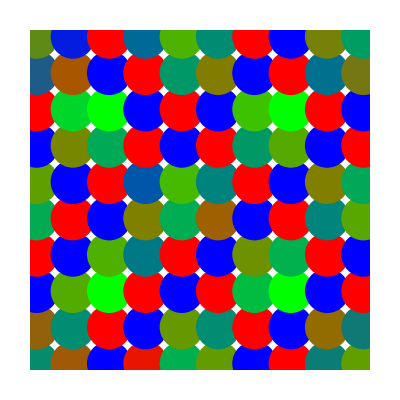
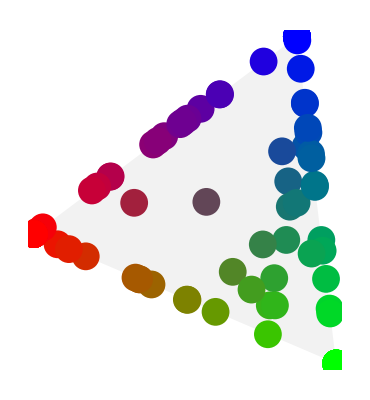
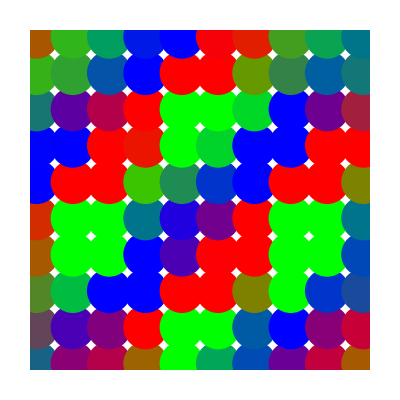

```mathematica
{Show[Graphics[{Opacity[0.05],Simplex[PrincipalComponents[#][[-3;;,;;2]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({PrincipalComponents[#][[;;-4,;;2]],#[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->True,ImageSize->Small]],Graphics[Flatten[{PointSize[.08],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({cellCoordinates2D,#[[;;-4]]}ᵀ)}]]}&/@geneExp2DG3Ts2
```

Figure 3A-E:

```mathematica
gridCells1D=GridGraph[{1,30}];
```

```mathematica
vs1D=VertexList[gridCells1D];
```

```mathematica
cellCoordinates1D=Table[x,{x,0,1,1/(30-1)}];
```

```mathematica
a=1;b=1;c=1;d=1;ω1=1;ω2=1;ω3=1;
res1D3T=NMaximize[{(Sum[((2-√((1-g1[x])^2+(g2[x])^2+(g3[x])^2))/2)(1-a x),{x,cellCoordinates1D}])^ω1(Sum[(2-√((g1[x])^2+(1-g2[x])^2+(g3[x])^2))/2(b x),{x,cellCoordinates1D}])^ω2(Sum[(2-√((g1[x])^2+(g2[x])^2+(1-g3[x])^2))/2,{x,cellCoordinates1D}])^ω3
,And@@(1≥#≥0&/@Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates1D}]])&&And@@(Total[#]==1&/@Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates1D}])},Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates1D}]]];
```

```mathematica
tri1D3T=PrincipalComponents[Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates1D}]/.res1D3T[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}]][[;;,;;2]];
```

```mathematica
geneExp1D3T=Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates1D}]/.res1D3T[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}];
```

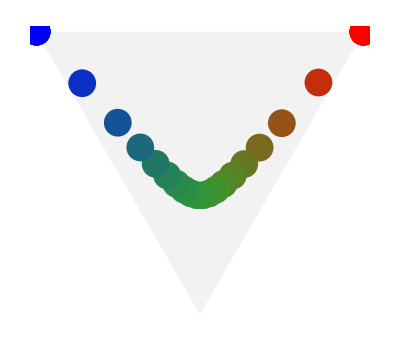

```mathematica
Show[Graphics[{Opacity[0.05],Simplex[tri1D3T[[-3;;]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({tri1D3T[[;;-4]],geneExp1D3T[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->True],PlotRange->All]
```

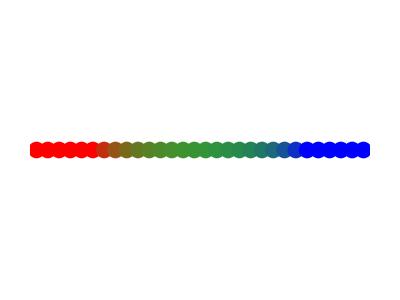

```mathematica
Graphics[Flatten[{PointSize[.03],{Blend[{Red,Blue,Green},#[[2]]],Point[{#[[1]],0}]}&/@({cellCoordinates1D,geneExp1D3T[[;;-4]]}ᵀ)}],AspectRatio->Full]
```

```mathematica
a=1;b=1;c=1;d=1;ω1=1;ω2=1;ω3=1;
res1K=NMaximize[{(Sum[((2-√((1-g1[x])^2+(g2[x])^2+(g3[x])^2))/2)(1-a x[[1]]),{x,cellCoordinates2D}])^ω1(Sum[(2-√((g1[x])^2+(1-g2[x])^2+(g3[x])^2))/2(1-b x[[2]]),{x,cellCoordinates2D}])^ω2(Sum[(2-√((g1[x])^2+(g2[x])^2+(1-g3[x])^2))/2,{x,cellCoordinates2D}])^ω3
,And@@(1≥#≥0&/@Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]])&&And@@(Total[#]==1&/@Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}])},Flatten[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]]];
```

```mathematica
tri1K=PrincipalComponents[Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.res1K[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}]][[;;,;;2]];
```

```mathematica
geneExp1K=Join[Chop[Table[{g1[x],g2[x],g3[x]},{x,cellCoordinates2D}]/.res1K[[2]],10^-2],{{1,0,0},{0,1,0},{0,0,1}}];
```

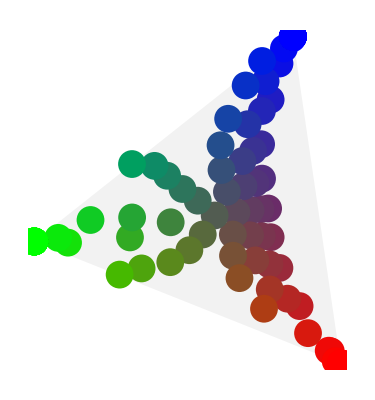

```mathematica
Show[Graphics[{Opacity[0.05],Simplex[tri1K[[-3;;]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({tri1K[[;;-4]],geneExp1K[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->True],PlotRange->All]
```

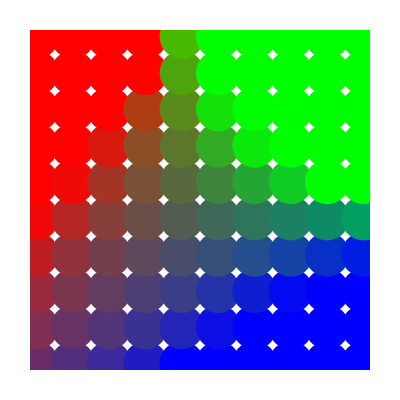

```mathematica
Graphics[Flatten[{PointSize[.08],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({cellCoordinates2D,#[[;;-4]]}ᵀ)}]]&@geneExp1K
```

```mathematica
geneExp1D3TsInt=Table[NMaximize[{(Sum[(2-((1-c1[i])^2+(c2[i])^2+(c3[i])^2))(1/2(2-(Mean@((2-((1-#[[1]])^2+(#[[2]])^2+(#[[3]])^2))&/@({c1[#],c2[#],c3[#]}&/@Complement[VertexList@NeighborhoodGraph[gridCells1D,i,j],{i}]))))),{i,vs1D}])
(Sum[(2-((c1[i])^2+(1-c2[i])^2+(c3[i])^2))(1/2(2-(Mean@((2-((#[[1]])^2+(1-#[[2]])^2+(#[[3]])^2))&/@({c1[#],c2[#],c3[#]}&/@Complement[VertexList@NeighborhoodGraph[gridCells1D,i,j],{i}]))))),{i,vs1D}])(Sum[(2-((c1[i])^2+(c2[i])^2+(1-c3[i])^2))(1/2(2-(Mean@((2-((#[[1]])^2+(#[[2]])^2+(1-#[[3]])^2))&/@({c1[#],c2[#],c3[#]}&/@Complement[VertexList@NeighborhoodGraph[gridCells1D,i,j],{i}]))))),{i,vs1D}])
,(And@@(1≥#>0&/@Flatten[Table[{c1[i],c2[i],c3[i]},{i,vs1D}]]))&&And@@(Total[#]==1&/@(Table[{c1[i],c2[i],c3[i]},{i,vs1D}]))},Flatten[Table[{c1[i],c2[i],c3[i]},{i,vs1D}]]],{j,{6}}];
```

```mathematica
geneExp1D3TsInt2=Join[Chop[Table[{c1[i],c2[i],c3[i]},{i,vs1D}]/.#,10^-2],{{1,0,0},{0,1,0},{0,0,1}}]&/@geneExp1D3TsInt[[;;,2]];
```

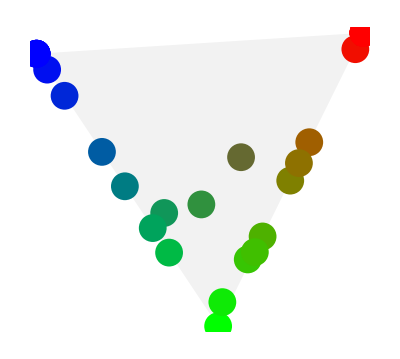
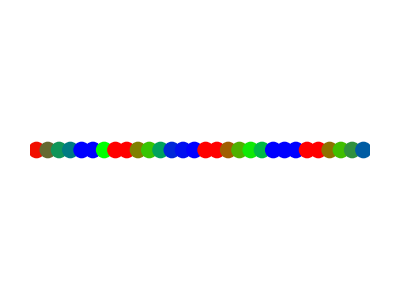

```mathematica
{Show[Graphics[{Opacity[0.05],Simplex[PrincipalComponents[#][[-3;;,;;2]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({PrincipalComponents[#][[;;-4,;;2]],#[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->True,ImageSize->Small]],Graphics[Flatten[{PointSize[.03],{Blend[{Red,Blue,Green},#[[2]]],Point[{#[[1]],0}]}&/@({cellCoordinates1D,#[[;;-4]]}ᵀ)}],AspectRatio->Full]}&/@geneExp1D3TsInt2
```

```mathematica
geneExp1D3TsInt=Table[NMaximize[{(Sum[(2-((1-c1[i])^2+(c2[i])^2+(c3[i])^2))((2-(Mean@((2-((1-#[[1]])^2+(#[[2]])^2+(#[[3]])^2))&/@({c1[#],c2[#],c3[#]}&/@Complement[VertexList@NeighborhoodGraph[gridCells1D,i,j],{i}]))))),{i,vs1D}])
(Sum[(2-((c1[i])^2+(1-c2[i])^2+(c3[i])^2))((2-(Mean@((2-((#[[1]])^2+(1-#[[2]])^2+(#[[3]])^2))&/@({c1[#],c2[#],c3[#]}&/@Complement[VertexList@NeighborhoodGraph[gridCells1D,i,j],{i}]))))),{i,vs1D}])(Sum[(2-((c1[i])^2+(c2[i])^2+(1-c3[i])^2))((2-(Mean@((2-((#[[1]])^2+(#[[2]])^2+(1-#[[3]])^2))&/@({c1[#],c2[#],c3[#]}&/@Complement[VertexList@NeighborhoodGraph[gridCells1D,i,j],{i}]))))),{i,vs1D}])
,(And@@(1≥#>0&/@Flatten[Table[{c1[i],c2[i],c3[i]},{i,vs1D}]]))&&And@@(Total[#]==1&/@(Table[{c1[i],c2[i],c3[i]},{i,vs1D}]))},Flatten[Table[{c1[i],c2[i],c3[i]},{i,vs1D}]]],{j,{6}}];
```

```mathematica
geneExp1D3TsInt2=Join[Chop[Table[{c1[i],c2[i],c3[i]},{i,vs1D}]/.#,10^-2],{{1,0,0},{0,1,0},{0,0,1}}]&/@geneExp1D3TsInt[[;;,2]];
```

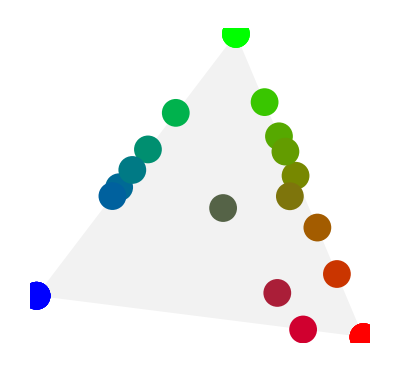
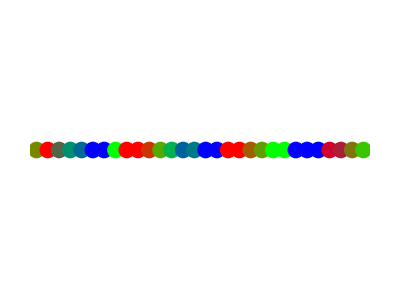

```mathematica
{Show[Graphics[{Opacity[0.05],Simplex[PrincipalComponents[#][[-3;;,;;2]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({PrincipalComponents[#][[;;-4,;;2]],#[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->True,ImageSize->Small]],Graphics[Flatten[{PointSize[.03],{Blend[{Red,Blue,Green},#[[2]]],Point[{#[[1]],0}]}&/@({cellCoordinates1D,#[[;;-4]]}ᵀ)}],AspectRatio->Full]}&/@geneExp1D3TsInt2
```

```mathematica
geneExp1D3TsInt=Table[NMaximize[{(Sum[(2-((1-c1[i])^2+(c2[i])^2+(c3[i])^2))/2((1-(Mean@((2-((1-#[[1]])^2+(#[[2]])^2+(#[[3]])^2))/2&/@({c1[#],c2[#],c3[#]}&/@Complement[VertexList@NeighborhoodGraph[gridCells1D,i,j],{i}]))))),{i,vs1D}])
(Sum[(2-((c1[i])^2+(1-c2[i])^2+(c3[i])^2))/2((1-(Mean@((2-((#[[1]])^2+(1-#[[2]])^2+(#[[3]])^2))/2&/@({c1[#],c2[#],c3[#]}&/@Complement[VertexList@NeighborhoodGraph[gridCells1D,i,j],{i}]))))),{i,vs1D}])(Sum[(2-((c1[i])^2+(c2[i])^2+(1-c3[i])^2))/2((1-(Mean@((2-((#[[1]])^2+(#[[2]])^2+(1-#[[3]])^2))/2&/@({c1[#],c2[#],c3[#]}&/@Complement[VertexList@NeighborhoodGraph[gridCells1D,i,j],{i}]))))),{i,vs1D}])
,(And@@(1≥#>0&/@Flatten[Table[{c1[i],c2[i],c3[i]},{i,vs1D}]]))&&And@@(Total[#]==1&/@(Table[{c1[i],c2[i],c3[i]},{i,vs1D}]))},Flatten[Table[{c1[i],c2[i],c3[i]},{i,vs1D}]]],{j,{6}}];
```

```mathematica
geneExp1D3TsInt2=Join[Chop[Table[{c1[i],c2[i],c3[i]},{i,vs1D}]/.#,10^-2],{{1,0,0},{0,1,0},{0,0,1}}]&/@geneExp1D3TsInt[[;;,2]];
```

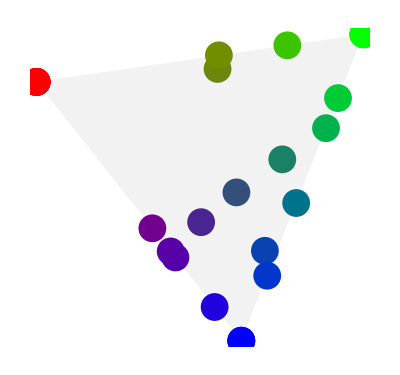
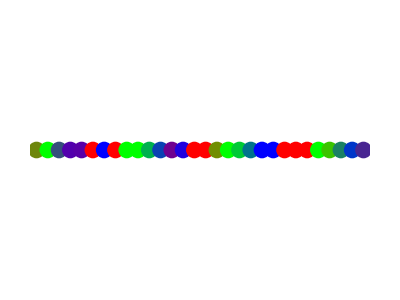

```mathematica
{Show[Graphics[{Opacity[0.05],Simplex[PrincipalComponents[#][[-3;;,;;2]]]},Frame->False],Graphics[Flatten[{PointSize[.05],{Blend[{Red,Blue,Green},#[[2]]],Point[#[[1]]]}&/@({PrincipalComponents[#][[;;-4,;;2]],#[[;;-4]]}ᵀ)}],AspectRatio->Automatic,Frame->True,ImageSize->Small]],Graphics[Flatten[{PointSize[.03],{Blend[{Red,Blue,Green},#[[2]]],Point[{#[[1]],0}]}&/@({cellCoordinates1D,#[[;;-4]]}ᵀ)}],AspectRatio->Full]}&/@geneExp1D3TsInt2
```

Figure 3H-I:

Raw sc data and zonation from Moore et al.:

```mathematica
rnaSeqData=Import["/supplementary_table_2_scRNAseq_UMI_table.tsv"];
```

```mathematica
zonation=Import["/supplementary_table_3_scRNAseq_tsne_coordinates_zones.tsv"];
```

```mathematica
zonation2=zonation[[2;;,4]]/.("V1"->1)/.("V2"->2)/.("V3"->3)/.("V4"->4)/.("V5"->5)/.("V6"->6)/.("Crypt"->0);
```

```mathematica
zonation3=Select[zonation2,#≠ 0&];
```

```mathematica
rnaSeqDataNoCrypt=Select[{rnaSeqData[[2;;,2;;]]ᵀ,zonation2}ᵀ,#[[2]]≠ 0&][[;;,1]];
```

```mathematica
NoZeroGenes=DeleteCases[Prepend[rnaSeqDataNoCrypt,rnaSeqData[[2;;,1]]]ᵀ,_?(Total[#[[2;;]]]==0&)];
```

```mathematica
geneExpEnt=Select[Prepend[N@(#/Total[#])&/@(NoZeroGenesᵀ[[2;;]]),NoZeroGenes[[;;,1]]]ᵀ,Mean[#[[2;;]]]>5 10^-6&]ᵀ[[2;;]];
```

```mathematica
NormgeneExpEntNoC=((#-Mean[#])/StandardDeviation[#]&/@(geneExpEntᵀ))ᵀ;
```

```mathematica
pcaEnt=PrincipalComponents[NormgeneExpEntNoC];
```

Use ParTi algorithm in matlab to find the archetypes and their errors(using PCHA):

```mathematica
arcs3EntNoCrypt=Import["/arcs3EntNoCrypt.mat"][[1]];
arcErr3EntNoCrypt=Import["/arcErr3EntNoCrypt.mat"];
```

```mathematica
arcsCoeffEnt=Table[Solve[{({#[[1]],#[[2]]}&/@pcaEnt[[;;,;;2]])[[i,1]]==a #[[1]]+b #[[2]]+c#[[3]]&@arcs3EntNoCrypt[[;;,1]],
({#[[1]],#[[2]]}&/@pcaEnt[[;;,;;2]])[[i,2]]==a #[[1]]+b #[[2]]+c#[[3]]&@arcs3EntNoCrypt[[;;,2]],a+b+c==1},{a,b,c}][[1,;;,2]],{i,1,Length[pcaEnt]}];
```

```mathematica
Show[{Graphics[{Opacity[0.02],ConvexHullMesh[arcs3EntNoCrypt[[;;,;;2]]]}],Graphics[{PointSize[.01],Flatten[{Blend[{Blue,Green,Red},#]&/@(arcsCoeffEnt),Point[#]&/@({#[[1]],#[[2]]}&/@pcaEnt[[;;,;;2]])}ᵀ]}],Graphics[{FaceForm[{#[[3]],Opacity[1]}],Translate[Rotate[Ellipsoid[{0,0},DiagonalMatrix[(Eigenvalues[#[[2]]])]],{{1,0},Eigenvectors[#[[2]]][[1]]}],#[[1]]]},AspectRatio->Automatic]}&/@({arcs3EntNoCrypt[[;;,;;2]],arcErr3EntNoCrypt[[;;,;;2,;;2]],{Blue,Green,Red}}ᵀ),PlotRange->All,Frame->False,AspectRatio->Automatic]
```

-Graphics-

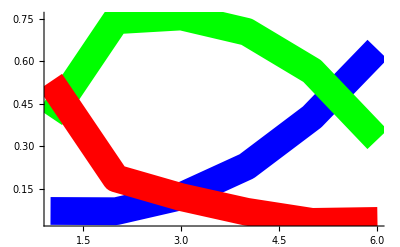

```mathematica
Show[ListLinePlot[Mean/@GatherBy[SortBy[{zonation3,arcsCoeffEnt[[;;,1]]}ᵀ,First],First][[;;,;;,2]],PlotRange->{{1,6},All},PlotStyle->{Thickness[.05],Blue}],ListLinePlot[Mean/@GatherBy[SortBy[{zonation3,arcsCoeffEnt[[;;,2]]}ᵀ,First],First][[;;,;;,2]],PlotRange->{{1,6},All},PlotStyle->{Thickness[.05],Green}],ListLinePlot[Mean/@GatherBy[SortBy[{zonation3,arcsCoeffEnt[[;;,3]]}ᵀ,First],First][[;;,;;,2]],PlotRange->{{1,6},All},PlotStyle->{Thickness[.05],Red}],PlotRange->All]
```

Figure 3K-L:

```mathematica
cells20=Import["/2020-09-14_Puck_200701_20_fibro_thr0.5_ct.csv"];
```

```mathematica
locs20=Import["/2020-09-14_Puck_200701_20_fibro_thr0.5_loc.csv"];
```

```mathematica
fibro20=Select[cells20[[2;;]],#[[Position[cells20[[1]],"Fibroblasts"][[1,1]]]]>.5&][[;;,1]];
```

```mathematica
expCRCHi20=Import["/expCRCHi20.mat"][[1]];
```

```mathematica
expCRCHi20PCA=PrincipalComponents[expCRCHi20];
```

```mathematica
Fibro203Arc=Import["/CRCFibro203Arcs_arc.mat"][[1]];
```

```mathematica
Fibro203ArcErrs=Import["/CRCFibro203Arcs_errs.mat"][[1,1]];
```

```mathematica
arcsCoeff203=Table[Solve[{({-#[[1]],-#[[2]]}&/@expCRCHi20PCA[[;;,;;2]])[[i,1]]==a #[[1]]+b #[[2]]+c#[[3]]&@Fibro203Arc[[;;,1]],
({-#[[1]],-#[[2]]}&/@expCRCHi20PCA[[;;,;;2]])[[i,2]]==a #[[1]]+b #[[2]]+c#[[3]]&@Fibro203Arc[[;;,2]],a+b+c==1},{a,b,c}][[1,;;,2]],{i,1,Length[expCRCHi20PCA]}];
```

```mathematica
Show[{Graphics[{Opacity[0.02],ConvexHullMesh[Fibro203Arc[[;;,;;2]]]}],Graphics[{PointSize[.02],Flatten[{Blend[{Red,Blue,Green},#]&/@(arcsCoeff203),Point[#]&/@({-#[[1]],-#[[2]]}&/@expCRCHi20PCA[[;;,;;3]])}ᵀ]}],Graphics[{FaceForm[{#[[3]],Opacity[1]}],Translate[Rotate[Ellipsoid[{0,0},DiagonalMatrix[((*.25*)Eigenvalues[#[[2]]])]],{{1,0},Eigenvectors[#[[2]]][[1]]}],#[[1]]]},AspectRatio->Automatic]}&/@({Fibro203Arc[[;;,;;2]],Fibro203ArcErrs[[;;,;;2,;;2]],{Red,Blue,Green}}ᵀ),PlotRange->All,Boxed->False,Frame->False]
```

-Graphics-

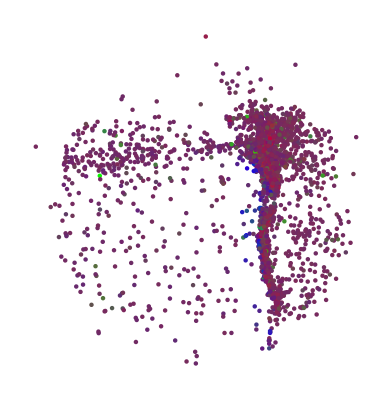

```mathematica
Graphics[{PointSize[.008],Flatten[{Blend[{Red,Blue,Green},#]&/@(arcsCoeff203),Point[#]&/@Select[locs20[[2;;]],MemberQ[fibro20,#[[1]]]&][[;;,2;;]]}ᵀ]},Frame->False]
```

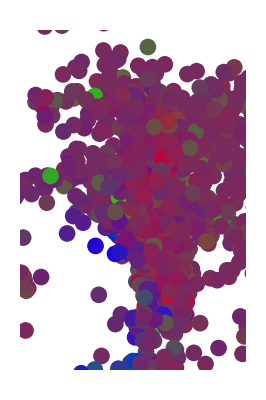

```mathematica
Graphics[{PointSize[.03],Flatten[{Blend[{Red,Blue,Green},#]&/@(arcsCoeff203),Point[#]&/@Select[locs20[[2;;]],MemberQ[fibro20,#[[1]]]&][[;;,2;;]]}ᵀ]},PlotRange->{{3600,4800},{3200,5000}}]
```

Figure 4:

```mathematica
colonSC5Arc=Import["/ColonSC5Arcs_arc.mat"][[1]];
```

```mathematica
colonSC5ArcErrs=Import["/ColonSC5Arcs_errs.mat"][[1,1]];
```

```mathematica
genesHi=Import["/colonSCGeneNames.txt","Data"][[;;,1]];
```

```mathematica
colonSCHi=Import["/colonSCData.mat"][[1]];
```

```mathematica
colonSCHiPCA=PrincipalComponents[colonSCHi];
```

```mathematica
Show[{Graphics3D[{Opacity[0],ConvexHullMesh[colonSC5Arc[[;;,;;3]]]}],Graphics3D[{PointSize[.01],Black,Point[#]&/@({-#[[1]],-#[[2]],-#[[3]]}&/@colonSCHiPCA[[;;,;;4]])}],Graphics3D[{FaceForm[{#[[3]],Opacity[0.5]}],Translate[Rotate[Ellipsoid[{0,0,0},DiagonalMatrix[(Eigenvalues[#[[2]]])]],{{1,0,0},Eigenvectors[#[[2]]][[1]]}],#[[1]]]},AspectRatio->Automatic]}&/@({colonSC5Arc[[;;,;;3]],colonSC5ArcErrs[[;;,;;3,;;3]],{Red,Blue,Green,Yellow,Purple}}ᵀ),PlotRange->All,Boxed->False]
```

-Graphics3D-

```mathematica
Table[Show[{Graphics3D[{Opacity[0],ConvexHullMesh[colonSC5Arc[[;;,;;3]]]}],Graphics3D[{PointSize[.02],Flatten[{ColorData["AvocadoColors"][#]&/@Rescale@(colonSCHi[[;;,Position[genesHi,g][[1,1]]]]),Point[#]&/@({-#[[1]],-#[[2]],-#[[3]]}&/@colonSCHiPCA[[;;,;;3]])}ᵀ]}],Graphics3D[{FaceForm[{#[[3]],Opacity[0.5]}],Translate[Rotate[Ellipsoid[{0,0,0},DiagonalMatrix[(Eigenvalues[#[[2]]])]],{{1,0,0},Eigenvectors[#[[2]]][[1]]}],#[[1]]]},AspectRatio->Automatic]}&/@({colonSC5Arc[[;;,;;3]],colonSC5ArcErrs[[;;,;;3,;;3]],{Red,Blue,Green,Yellow,Purple}}ᵀ),PlotRange->All,Boxed->False,PlotLabel->g],{g,{"Bmp7","Bmpr1a","Wnt2","Fzd1","Dll1","Notch2"}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
mouseLRPairs=Import["/mouse_lr_pair.txt","Data"];
```

```mathematica
ligRecPairs=mouseLRPairs[[2;;,{2,3}]];
ligRecPairs2=Map[StringJoin[StringTake[#,1],ToLowerCase[StringTake[#,2;;]]]&,ligRecPairs,{2}];
```

```mathematica
ligColonSC=Intersection[genesHi,ligRecPairs2[[;;,1]]];
```

```mathematica
colonSC5EnrGenes=Import["/ColonSC5ArcsGenes_continuous_significant.csv"];
```

```mathematica
ligEnrColonSC=Select[ligColonSC,Position[colonSC5EnrGenes,#]≠{}&];
```

```mathematica
ligEnrColonSC2=SortBy[(colonSC5EnrGenes[[#,;;4]]&/@Position[colonSC5EnrGenes,#][[;;,1]]&/@ligEnrColonSC)[[;;,1]],-#[[4]]&][[;;,;;2]];
```

```mathematica
recColonSC=Intersection[genesHi,ligRecPairs2[[;;,2]]];
```

```mathematica
recEnrColonSC=Select[recColonSC,Position[colonSC5EnrGenes,#]≠{}&];
```

```mathematica
recEnrColonSC2=SortBy[(colonSC5EnrGenes[[#,;;4]]&/@Position[colonSC5EnrGenes,#][[;;,1]]&/@recEnrColonSC)[[;;,1]],-#[[4]]&][[;;,;;2]];
```

```mathematica
ligRecPairsColonSC=Union@Select[ligRecPairs2,Length[DeleteCases[Position[genesHi,#]&/@#,{}]]>1&];
```

```mathematica
ligRecEnrColonSC=Select[ligRecPairsColonSC,Length[DeleteCases[Position[colonSC5EnrGenes,#]&/@#,{}]]>1&];
```

```mathematica
ligRecEnrColonSC2=SortBy[{SortBy[#,-#[[4]]&][[1,;;2]]&/@(colonSC5EnrGenes[[#,;;4]]&/@Position[colonSC5EnrGenes,#][[;;,1]]&/@ligRecEnrColonSC[[;;,1]]),SortBy[#,-#[[4]]&][[1,;;2]]&/@(colonSC5EnrGenes[[#,;;4]]&/@Position[colonSC5EnrGenes,#][[;;,1]]&/@ligRecEnrColonSC[[;;,2]])}ᵀ,#[[;;,1]]&];
```

```mathematica
<<IGraphM`
```

IGraph/M 0.4 (April 2, 2020)
Evaluate IGDocumentation[] to get started.

```mathematica
gColonSC5=Graph[Range@5,DirectedEdge@@@(#[[1]]&/@Tally[ligRecEnrColonSC2[[;;,;;,1]]]),EdgeWeight->Thread[DirectedEdge@@@(#[[1]]&/@Tally[ligRecEnrColonSC2[[;;,;;,1]]])->Tally[ligRecEnrColonSC2[[;;,;;,1]]][[;;,2]]],VertexStyle->{1->Red,2->Blue,3->Green,4->Yellow,5->Purple},VertexSize->0.5,EdgeShapeFunction->GraphElementData[{"CarvedArrow","ArrowSize"->.05}]];
```

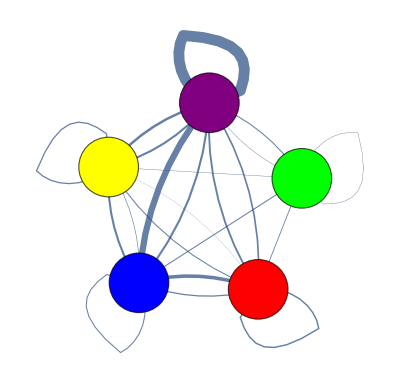

```mathematica
IGEdgeMap[AbsoluteThickness[.15 #]&,EdgeStyle->IGEdgeProp[EdgeWeight],gColonSC5]
```

```mathematica
locs=Import["/sc_on_ss_pred_loc.csv"];
```

```mathematica
tasks=Import["/sc_on_ss_pred_tasks.csv"];
```

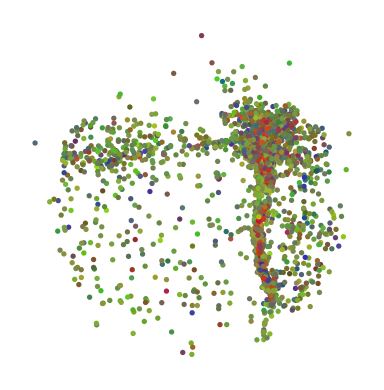

```mathematica
Graphics[{PointSize[.01],Flatten[{Blend[{Red,Blue,Green,Yellow,Purple},#]&/@(tasks[[2;;,2;;]]),Point[#]&/@(locs[[2;;,2;;]])}ᵀ]}]
```

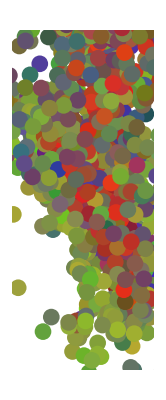

```mathematica
Graphics[{PointSize[.03],Flatten[{Blend[{Red,Blue,Green,Yellow,Purple},#]&/@(tasks[[2;;,2;;]]),Point[#]&/@(locs[[2;;,2;;]])}ᵀ]},PlotRange->{{4000,4500},{3300,4500}}]
```

Figure 5:

```mathematica
control5Arc=Import["/controlSanity945C6934G_5ArcsSisal_arc.mat"][[1]];
```

```mathematica
control5ArcErrs=Import["/controlSanity945C6934G_5ArcsSisal_errs.mat"][[1,1]];
```

```mathematica
FibMyoControlHiVarGenes=Import["/FibMyoControlSanityGenes6934G.txt","Data"][[;;,1]];
```

```mathematica
FibMyoControlHiVarData2=Import["/FibMyoControlSanityData945C6934G.mat"][[1]];
```

```mathematica
FibMyoControlHiVarPCA2=PrincipalComponents[FibMyoControlHiVarData2];
```

```mathematica
Show[ListPointPlot3D[{-#[[1]],-#[[2]],-#[[3]]}&/@FibMyoControlHiVarPCA2[[;;,;;3]],PlotStyle->{PointSize[.01],Black},PlotRange->All],{Graphics3D[{Opacity[0],ConvexHullMesh[control5Arc[[;;,;;3]]]}],Graphics3D[{FaceForm[{#[[3]],Opacity[0.5]}],Translate[Rotate[Ellipsoid[{0,0,0},DiagonalMatrix[(Eigenvalues[#[[2]]])]],{{1,0,0},Eigenvectors[#[[2]]][[1]]}],#[[1]]]},AspectRatio->Automatic]}&/@({control5Arc[[;;,;;3]],control5ArcErrs[[;;,;;3,;;3]],{Yellow,Blue,Green,Red,Purple}}ᵀ),PlotRange->All,Boxed->False,PlotLabel->"Control Fibroblasts Myofibroblasts",Axes->False,BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
control5ArcsEnrGenesTable=Import["/controlSanity945C3942G_5ArcsSisal_continuous_significant.csv"];
```

```mathematica
humanLRPairs=Import["/human_lr_pair.txt","Data"];
```

```mathematica
humanLRPairs2=humanLRPairs[[2;;,{2,3}]];
```

```mathematica
ligFibMyoControl=Intersection[FibMyoControlHiVarGenes,humanLRPairs2[[;;,1]]];
```

```mathematica
ligEnrControl=Select[ligFibMyoControl,Position[control5ArcsEnrGenesTable,#]≠{}&];
```

```mathematica
ligEnrControl2=SortBy[(control5ArcsEnrGenesTable[[#,;;4]]&/@Position[control5ArcsEnrGenesTable,#][[;;,1]]&/@ligEnrControl)[[;;,1]],-#[[4]]&][[;;,;;2]];
```

```mathematica
recFibMyoControl=Intersection[FibMyoControlHiVarGenes,humanLRPairs2[[;;,2]]];
```

```mathematica
recEnrControl=Select[recFibMyoControl,Position[control5ArcsEnrGenesTable,#]≠{}&];
```

```mathematica
recEnrControl2=SortBy[(control5ArcsEnrGenesTable[[#,;;4]]&/@Position[control5ArcsEnrGenesTable,#][[;;,1]]&/@recEnrControl)[[;;,1]],-#[[4]]&][[;;,;;2]];
```

```mathematica
ligRecPairsFibControl=Union@Select[humanLRPairs2,Length[DeleteCases[Position[FibMyoControlHiVarGenes,#]&/@#,{}]]>1&];
```

```mathematica
ligRecEnrControl=Select[ligRecPairsFibControl,Length[DeleteCases[Position[control5ArcsEnrGenesTable,#]&/@#,{}]]>1&];
```

```mathematica
ligRecEnrControl2=SortBy[{SortBy[#,-#[[4]]&][[1,;;2]]&/@(control5ArcsEnrGenesTable[[#,;;4]]&/@Position[control5ArcsEnrGenesTable,#][[;;,1]]&/@ligRecEnrControl[[;;,1]]),SortBy[#,-#[[4]]&][[1,;;2]]&/@(control5ArcsEnrGenesTable[[#,;;4]]&/@Position[control5ArcsEnrGenesTable,#][[;;,1]]&/@ligRecEnrControl[[;;,2]])}ᵀ,#[[;;,1]]&];
```

```mathematica
gLungFib=Graph[Range@5,DirectedEdge@@@(#[[1]]&/@Tally[ligRecEnrControl2[[;;,;;,1]]]),EdgeWeight->Thread[DirectedEdge@@@(#[[1]]&/@Tally[ligRecEnrControl2[[;;,;;,1]]])->Tally[ligRecEnrControl2[[;;,;;,1]]][[;;,2]]],VertexStyle->{1->Yellow,2->Blue,3->Green,4->Red,5->Purple},VertexSize->0.5];
```

```mathematica
IGEdgeMap[AbsoluteThickness[.5 #]&,EdgeStyle->IGEdgeProp[EdgeWeight],gLungFib]
```

-Graphics-

```mathematica
MonoMacsControlSanityHi=Import["/MonoMacsControlSampSanity.mat"][[1]];
```

```mathematica
MonoMacsControlHiGenes=Import["/MonoMacsControlSampHiGenes.txt","Data"][[;;,1]];
```

```mathematica
MonoMacsControlSISAL4Arcs=Import["/MacsSISAL4Arcs_arc.mat"][[1]];
```

```mathematica
MonoMacsControlSISAL4ArcsErrs=Import["/MacsSISAL4Arcs_errs.mat"][[1,1]];
```

```mathematica
MonoMacsControlSanityHiPCA=PrincipalComponents[MonoMacsControlSanityHi];
```

```mathematica
Show[ListPointPlot3D[{#[[1]],#[[2]],-#[[3]]}&/@MonoMacsControlSanityHiPCA[[;;,;;3]],PlotStyle->{PointSize[.005],Black},PlotRange->All],{Graphics3D[{Opacity[0],ConvexHullMesh[MonoMacsControlSISAL4Arcs[[;;,;;3]]]}],Graphics3D[{FaceForm[{#[[3]],Opacity[0.5]}],Translate[Rotate[Ellipsoid[{0,0,0},DiagonalMatrix[(.2Eigenvalues[#[[2]]])]],{{1,0,0},Eigenvectors[#[[2]]][[1]]}],#[[1]]]},AspectRatio->Automatic]}&/@({MonoMacsControlSISAL4Arcs[[;;,;;3]],MonoMacsControlSISAL4ArcsErrs[[;;,;;3,;;3]],{Yellow,Red,Blue,Green}}ᵀ),PlotRange->All,Boxed->False,PlotLabel->"Control Monocytes Macrophages",Axes->False,BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
MonoMacsControlSISAL4ArcsGenes=Import ["/MacsSISALGenes4Arcs_continuous_significant.csv"];
```

```mathematica
ligMonoMacsControl=Intersection[MonoMacsControlHiGenes,humanLRPairs2[[;;,1]]];
```

```mathematica
ligEnrControl=Select[ligMonoMacsControl,Position[MonoMacsControlSISAL4ArcsGenes,#]≠{}&];
```

```mathematica
ligEnrControl2=SortBy[(MonoMacsControlSISAL4ArcsGenes[[#,;;4]]&/@Position[MonoMacsControlSISAL4ArcsGenes,#][[;;,1]]&/@ligEnrControl)[[;;,1]],-#[[4]]&][[;;,;;2]];
```

```mathematica
recMonoMacsControl=Intersection[MonoMacsControlHiGenes,humanLRPairs2[[;;,2]]];
```

```mathematica
recEnrControl=Select[recMonoMacsControl,Position[MonoMacsControlSISAL4ArcsGenes,#]≠{}&];
```

```mathematica
recEnrControl2=SortBy[(MonoMacsControlSISAL4ArcsGenes[[#,;;4]]&/@Position[MonoMacsControlSISAL4ArcsGenes,#][[;;,1]]&/@recEnrControl)[[;;,1]],-#[[4]]&][[;;,;;2]];
```

```mathematica
ligRecPairsMonoMacsControl=Union@Select[humanLRPairs2,Length[DeleteCases[Position[MonoMacsControlHiGenes,#]&/@#,{}]]>1&];
```

```mathematica
ligRecEnrControl=Select[ligRecPairsMonoMacsControl,Length[DeleteCases[Position[MonoMacsControlSISAL4ArcsGenes,#]&/@#,{}]]>1&];
```

```mathematica
ligRecEnrControl2=SortBy[{SortBy[#,-#[[4]]&][[1,;;2]]&/@(MonoMacsControlSISAL4ArcsGenes[[#,;;4]]&/@Position[MonoMacsControlSISAL4ArcsGenes,#][[;;,1]]&/@ligRecEnrControl[[;;,1]]),SortBy[#,-#[[4]]&][[1,;;2]]&/@(MonoMacsControlSISAL4ArcsGenes[[#,;;4]]&/@Position[MonoMacsControlSISAL4ArcsGenes,#][[;;,1]]&/@ligRecEnrControl[[;;,2]])}ᵀ,#[[;;,1]]&];
```

```mathematica
gLungMac=Graph[Range@4,DirectedEdge@@@(#[[1]]&/@Tally[ligRecEnrControl2[[;;,;;,1]]]),EdgeWeight->Thread[DirectedEdge@@@(#[[1]]&/@Tally[ligRecEnrControl2[[;;,;;,1]]])->Tally[ligRecEnrControl2[[;;,;;,1]]][[;;,2]]],VertexStyle->{1->Yellow,2->Red,3->Blue,4->Green},VertexSize->0.5];
```

```mathematica
IGEdgeMap[AbsoluteThickness[.5 #]&,EdgeStyle->IGEdgeProp[EdgeWeight],gLungMac]
```

-Graphics-

```mathematica
Show[{Graphics[{FaceForm[{#[[3]],Opacity[1]}],Translate[Rotate[Ellipsoid[{0,0},DiagonalMatrix[(Eigenvalues[#[[2]]])]],{{1,0},Eigenvectors[#[[2]]][[1]]}],#[[1]]]},AspectRatio->Automatic],Graphics[{Opacity[0],EdgeForm[Black],Simplex[arcs3EntNoCrypt]}],Graphics[{Point[#],Black,PointSize[0.01]}&/@pcaEnt[[;;,;;2]],AspectRatio->Automatic]}&/@({arcs3EntNoCrypt,arcErr3EntNoCrypt,{Red,Darker[Green],Blue}}ᵀ),PlotRange->All,Frame->False]
```

-Graphics-

```mathematica
genesEnt=Select[Prepend[N@(#/Total[#])&/@(NoZeroGenesᵀ[[2;;]]),NoZeroGenes[[;;,1]]]ᵀ,Mean[#[[2;;]]]>5 10^-6&]ᵀ[[1]];
```

```mathematica
EntEnrGenes=Import["/EntNorm3ArchsNoCrypt_continuous_significant.csv"];
```

```mathematica
ligEnt=Intersection[genesEnt,ligRecPairs2[[;;,1]]];
```

```mathematica
ligEnrEnt=Select[ligEnt,Position[EntEnrGenes,#]≠{}&];
```

```mathematica
ligEnrEnt2=SortBy[(EntEnrGenes[[#,;;4]]&/@Position[EntEnrGenes,#][[;;,1]]&/@ligEnrEnt)[[;;,1]],-#[[4]]&][[;;,;;2]];
```

```mathematica
recEnt=Intersection[genesEnt,ligRecPairs2[[;;,2]]];
```

```mathematica
recEnrEnt=Select[recEnt,Position[EntEnrGenes,#]≠{}&];
```

```mathematica
recEnrEnt2=SortBy[(EntEnrGenes[[#,;;4]]&/@Position[EntEnrGenes,#][[;;,1]]&/@recEnrEnt)[[;;,1]],-#[[4]]&][[;;,;;2]];
```

```mathematica
ligRecPairsEnt=Union@Select[ligRecPairs2,Length[DeleteCases[Position[genesEnt,#]&/@#,{}]]>1&];
```

```mathematica
ligRecEnrEnt=Select[ligRecPairsEnt,Length[DeleteCases[Position[EntEnrGenes,#]&/@#,{}]]>1&];
```

```mathematica
ligRecEnrEnt2=SortBy[{SortBy[#,-#[[4]]&][[1,;;2]]&/@(EntEnrGenes[[#,;;4]]&/@Position[EntEnrGenes,#][[;;,1]]&/@ligRecEnrEnt[[;;,1]]),SortBy[#,-#[[4]]&][[1,;;2]]&/@(EntEnrGenes[[#,;;4]]&/@Position[EntEnrGenes,#][[;;,1]]&/@ligRecEnrEnt[[;;,2]])}ᵀ,#[[;;,1]]&];
```

```mathematica
gEnt=Graph[Range@3,DirectedEdge@@@(#[[1]]&/@Tally[ligRecEnrEnt2[[;;,;;,1]]]),EdgeWeight->Thread[DirectedEdge@@@(#[[1]]&/@Tally[ligRecEnrEnt2[[;;,;;,1]]])->Tally[ligRecEnrEnt2[[;;,;;,1]]][[;;,2]]],VertexStyle->{1->Red,2->Green,3->Blue},VertexSize->0.3];
```

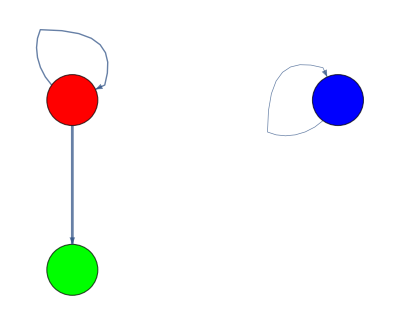

```mathematica
IGEdgeMap[AbsoluteThickness[.5 #]&,EdgeStyle->IGEdgeProp[EdgeWeight],gEnt]
```

Figure S4:

```mathematica
expCRCHiExp=Import["/expCRCHi.mat"][[1]];
```

```mathematica
expCRCHiExpPCA=PrincipalComponents[expCRCHiExp];
```

```mathematica
FibroE3Arc=Import["/CRCFibroExp3Arcs_arc.mat"][[1]];
```

```mathematica
FibroE3ArcErrs=Import["/CRCFibroExp3Arcs_errs.mat"][[1,1]];
```

```mathematica
arcs3Coeff=Table[Solve[{({#[[1]],-#[[2]]}&/@expCRCHiExpPCA[[;;,;;2]])[[i,1]]==a #[[1]]+b #[[2]]+c#[[3]]&@FibroE3Arc[[;;,1]],
({#[[1]],-#[[2]]}&/@expCRCHiExpPCA[[;;,;;2]])[[i,2]]==a #[[1]]+b #[[2]]+c#[[3]]&@FibroE3Arc[[;;,2]],a+b+c==1},{a,b,c}][[1,;;,2]],{i,1,Length[expCRCHiExpPCA]}];
```

```mathematica
Show[{Graphics[{Opacity[0.03],ConvexHullMesh[FibroE3Arc[[;;,;;2]]]}],Graphics[{PointSize[.01],Flatten[{Blend[{Blue,Red,Green},#]&/@(arcs3Coeff),Point[#]&/@({#[[1]],-#[[2]]}&/@expCRCHiExpPCA[[;;,;;2]])}ᵀ]}],Graphics[{FaceForm[{#[[3]],Opacity[0.5]}],Translate[Rotate[Ellipsoid[{0,0},DiagonalMatrix[(Eigenvalues[#[[2]]])]],{{1,0},Eigenvectors[#[[2]]][[1]]}],#[[1]]]},AspectRatio->Automatic]}&/@({FibroE3Arc[[;;,;;2]],FibroE3ArcErrs[[;;,;;2,;;2]],{Blue,Red,Green}}ᵀ),PlotRange->All,Frame->False]
```

-Graphics-

```mathematica
cells=Import["/2020-09-14_Puck_200701_23_fibro_thr0.5_ct.csv"];
```

```mathematica
locs=Import["/2020-09-14_Puck_200701_23_fibro_thr0.5_loc.csv"];
```

```mathematica
fibro=Select[cells[[2;;]],#[[Position[cells[[1]],"Fibroblasts"][[1,1]]]]>.5&][[;;,1]];
```

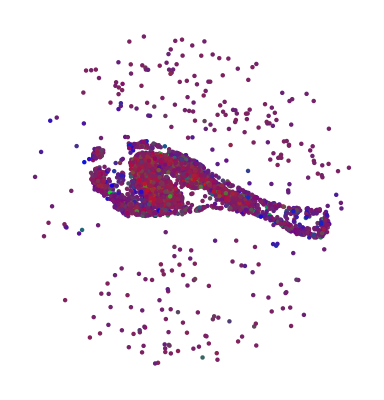

```mathematica
Graphics[{PointSize[.008],Flatten[{Blend[{Blue,Red,Green},#]&/@(arcs3Coeff),Point[#]&/@Select[locs[[2;;]],MemberQ[fibro,#[[1]]]&][[;;,2;;]]}ᵀ]},Frame->False]
```

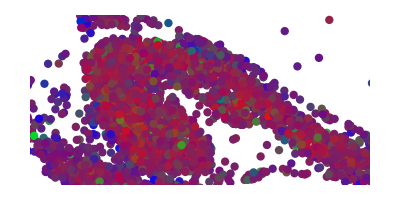

```mathematica
Graphics[{PointSize[.015],Flatten[{Blend[{Blue,Red,Green},#]&/@(arcs3Coeff),Point[#]&/@Select[locs[[2;;]],MemberQ[fibro,#[[1]]]&][[;;,2;;]]}ᵀ]},PlotRange->{{2000,4000},{3000,4000}}]
```

Figure S6:

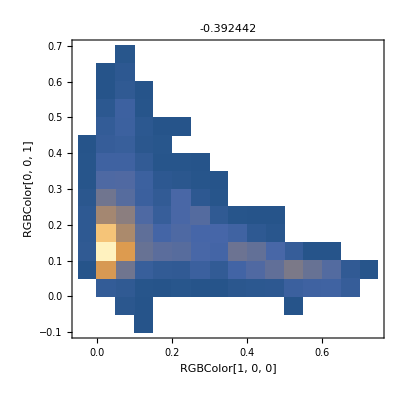
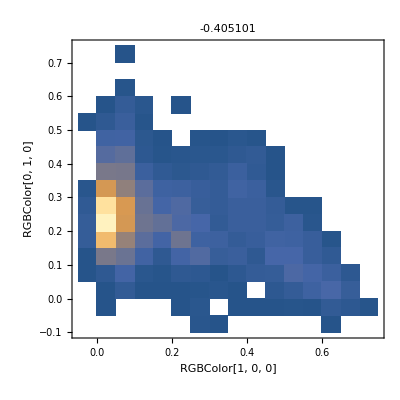
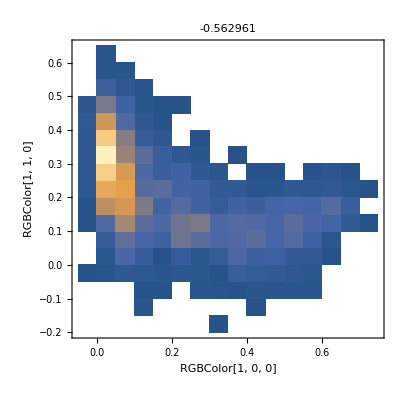
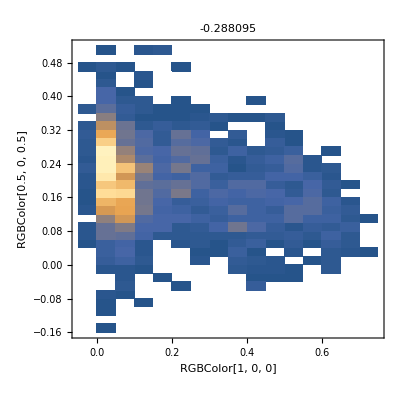
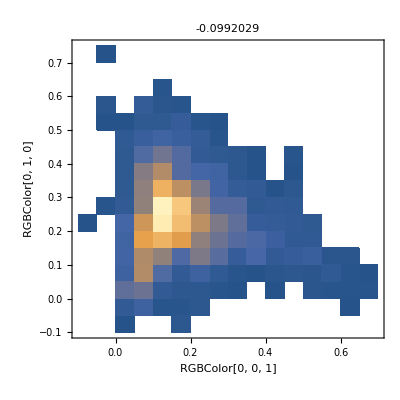
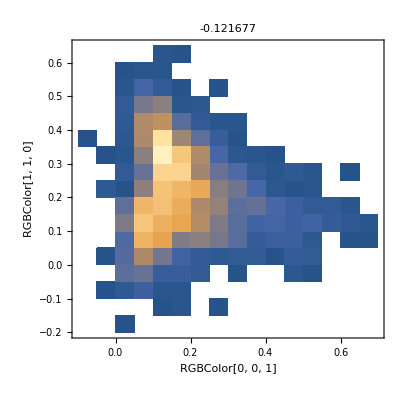
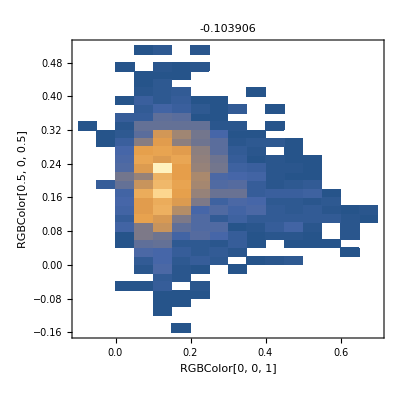
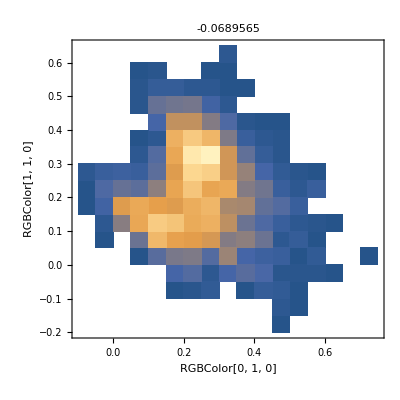

```mathematica
DensityHistogram[#[[2]]ᵀ,FrameLabel->#[[1]],PlotRange->All,PlotLabel->PearsonCorrelationTest[#[[2,1]],#[[2,2]],"TestStatistic"]]&/@({Subsets[{Red,Blue,Green,Yellow,Purple},{2}],Subsets[(tasks[[2;;,2;;]]ᵀ),{2}]}ᵀ)//Quiet
```

Figure S7:

```mathematica
weights=Thread[DirectedEdge@@@(#[[1]]&/@Tally[ligRecEnrColonSC2[[;;,;;,1]]])->Tally[ligRecEnrColonSC2[[;;,;;,1]]][[;;,2]]];
```

```mathematica
ligNumEnr=SortBy[Tally[ligEnrColonSC2[[;;,1]]],First][[;;,2]];
```

```mathematica
recNumEnr=SortBy[Tally[recEnrColonSC2[[;;,1]]],First][[;;,2]];
```

```mathematica
gColonSC5Norm=Graph[Range@5,DirectedEdge@@@(#[[1]]&/@Tally[ligRecEnrColonSC2[[;;,;;,1]]]),EdgeWeight->Thread[weights[[;;,1]]->(N@((#[[2]])/(ligNumEnr[[#[[1,1]]]]+recNumEnr[[#[[1,2]]]]))&/@weights)],VertexStyle->{1->Red,2->Blue,3->Green,4->Yellow,5->Purple},VertexSize->0.5,EdgeShapeFunction->GraphElementData[{"CarvedArrow","ArrowSize"->.05}]];
```

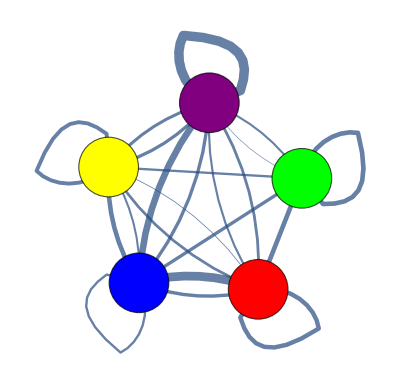

```mathematica
IGEdgeMap[AbsoluteThickness[20#]&,EdgeStyle->IGEdgeProp[EdgeWeight],gColonSC5Norm]
```

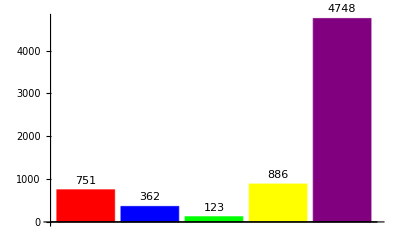

```mathematica
BarChart[Table[Length@Select[colonSC5EnrGenes,#[[1]]==i&],{i,1,5}],ChartStyle->{Red,Blue,Green,Yellow,Purple},LabelingFunction->Above]
```

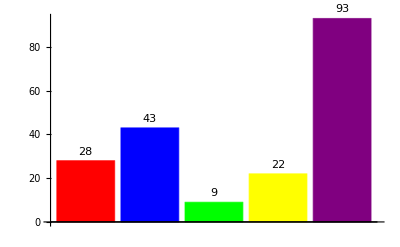

```mathematica
BarChart[Table[Length@Intersection[Union[ligRecPairs2[[;;,1]]],Select[colonSC5EnrGenes,#[[1]]==i&][[;;,2]]],{i,1,5}],ChartStyle->{Red,Blue,Green,Yellow,Purple},LabelingFunction->Above]
```

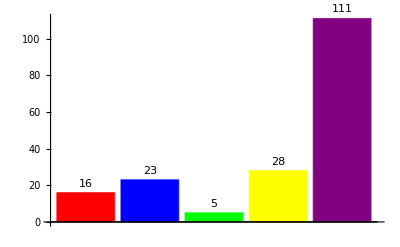

```mathematica
BarChart[Table[Length@Intersection[Union[ligRecPairs2[[;;,2]]],Select[colonSC5EnrGenes,#[[1]]==i&][[;;,2]]],{i,1,5}],ChartStyle->{Red,Blue,Green,Yellow,Purple},LabelingFunction->Above]
```

Figure S8:

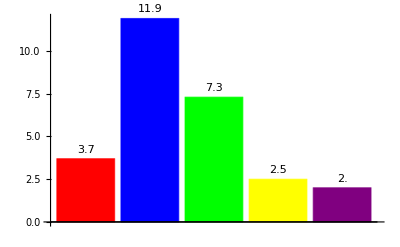

```mathematica
BarChart[Table[N@Round[100(Length@Intersection[Union[ligRecPairs2[[;;,1]]],Select[colonSC5EnrGenes,#[[1]]==i&][[;;,2]]])/(Length@Select[colonSC5EnrGenes,#[[1]]==i&]),.1],{i,1,5}],ChartStyle->{Red,Blue,Green,Yellow,Purple},LabelingFunction->Above]
```

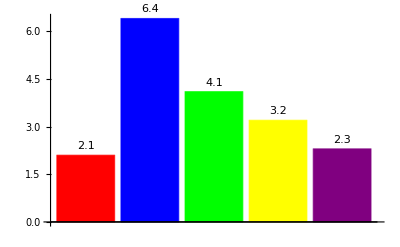

```mathematica
BarChart[Table[N@Round[100(Length@Intersection[Union[ligRecPairs2[[;;,2]]],Select[colonSC5EnrGenes,#[[1]]==i&][[;;,2]]])/(Length@Select[colonSC5EnrGenes,#[[1]]==i&]),.1],{i,1,5}],ChartStyle->{Red,Blue,Green,Yellow,Purple},LabelingFunction->Above]
```

```mathematica
enrGenesWGenArcs=Import["/GenArcsColonSCGenes_continuous_significant.csv"];
```

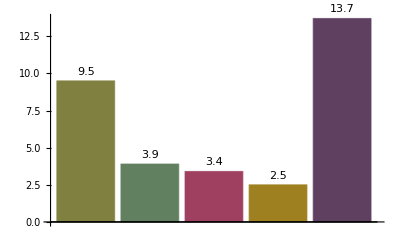

```mathematica
BarChart[Table[N@Round[100(Length@Intersection[Union[ligRecPairs2[[;;,1]]],Select[enrGenesWGenArcs,#[[1]]==i&][[;;,2]]])/(Length@Select[enrGenesWGenArcs,#[[1]]==i&]),.1],{i,1,5}],ChartStyle->Blend/@Subsets[{Yellow,Blue,Green,Red,Purple},{4}],LabelingFunction->Above]
```

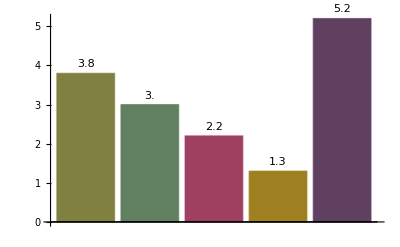

```mathematica
BarChart[Table[N@Round[100(Length@Intersection[Union[ligRecPairs2[[;;,2]]],Select[enrGenesWGenArcs,#[[1]]==i&][[;;,2]]])/(Length@Select[enrGenesWGenArcs,#[[1]]==i&]),.1],{i,1,5}],ChartStyle->Blend/@Subsets[{Yellow,Blue,Green,Red,Purple},{4}],LabelingFunction->Above]
```

```mathematica
ligEnrColonSC=Select[ligColonSC,Position[enrGenesWGenArcs,#]≠{}&];
```

```mathematica
ligEnrColonSC2=SortBy[(enrGenesWGenArcs[[#,;;4]]&/@Position[enrGenesWGenArcs,#][[;;,1]]&/@ligEnrColonSC)[[;;,1]],-#[[4]]&][[;;,;;2]];
```

```mathematica
recEnrColonSC=Select[recColonSC,Position[enrGenesWGenArcs,#]≠{}&];
```

```mathematica
recEnrColonSC2=SortBy[(enrGenesWGenArcs[[#,;;4]]&/@Position[enrGenesWGenArcs,#][[;;,1]]&/@recEnrColonSC)[[;;,1]],-#[[4]]&][[;;,;;2]];
```

```mathematica
ligRecEnrColonSC=Select[ligRecPairsColonSC,Length[DeleteCases[Position[enrGenesWGenArcs,#]&/@#,{}]]>1&];
```

```mathematica
ligRecEnrColonSC2=SortBy[{SortBy[#,-#[[4]]&][[1,;;2]]&/@(enrGenesWGenArcs[[#,;;4]]&/@Position[enrGenesWGenArcs,#][[;;,1]]&/@ligRecEnrColonSC[[;;,1]]),SortBy[#,-#[[4]]&][[1,;;2]]&/@(enrGenesWGenArcs[[#,;;4]]&/@Position[enrGenesWGenArcs,#][[;;,1]]&/@ligRecEnrColonSC[[;;,2]])}ᵀ,#[[;;,1]]&];
```

```mathematica
gColonSC=Graph[Range@5,DirectedEdge@@@(#[[1]]&/@Tally[ligRecEnrColonSC2[[;;,;;,1]]]),EdgeWeight->Thread[DirectedEdge@@@(#[[1]]&/@Tally[ligRecEnrColonSC2[[;;,;;,1]]])->Tally[ligRecEnrColonSC2[[;;,;;,1]]][[;;,2]]],VertexStyle->Thread[Range@5->Blend/@Subsets[{Yellow,Blue,Green,Red,Purple},{4}]],VertexSize->0.3];
```

```mathematica
IGEdgeMap[AbsoluteThickness[.15 #]&,EdgeStyle->IGEdgeProp[EdgeWeight],gColonSC]
```

-Graphics-

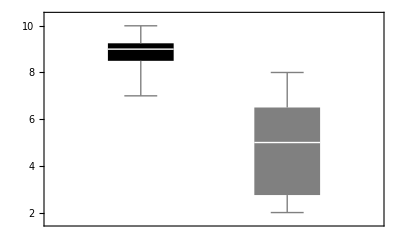

```mathematica
BoxWhiskerChart[{VertexDegree[gColonSC5],VertexDegree[gColonSC]},ChartStyle->{Black,Gray}]
```

```mathematica
enrGenesGenArcs=Import["/GenArcsFibMyoGenes_continuous_significant.csv"];
```

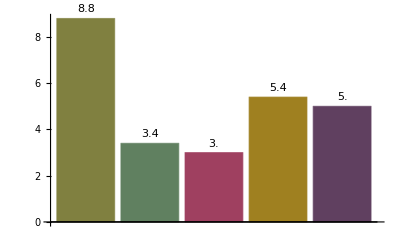

```mathematica
BarChart[Table[N@Round[100(Length@Intersection[Union[ligRecPairs[[;;,1]]],Select[enrGenesGenArcs,#[[1]]==i&][[;;,2]]])/(Length@Select[enrGenesGenArcs,#[[1]]==i&]),.1],{i,1,5}],ChartStyle->Blend/@Subsets[{Yellow,Blue,Green,Red,Purple},{4}],LabelingFunction->Above]
```

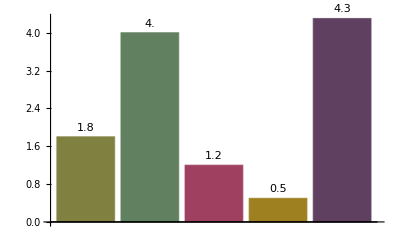

```mathematica
BarChart[Table[N@Round[100(Length@Intersection[Union[ligRecPairs[[;;,2]]],Select[enrGenesGenArcs,#[[1]]==i&][[;;,2]]])/(Length@Select[enrGenesGenArcs,#[[1]]==i&]),.1],{i,1,5}],ChartStyle->Blend/@Subsets[{Yellow,Blue,Green,Red,Purple},{4}],LabelingFunction->Above]
```

```mathematica
ligEnrControl=Select[ligFibMyoControl,Position[enrGenesGenArcs,#]≠{}&];
```

```mathematica
ligEnrControl2=SortBy[(enrGenesGenArcs[[#,;;4]]&/@Position[enrGenesGenArcs,#][[;;,1]]&/@ligEnrControl)[[;;,1]],-#[[4]]&][[;;,;;2]];
```

```mathematica
recEnrControl=Select[recFibMyoControl,Position[enrGenesGenArcs,#]≠{}&];
```

```mathematica
recEnrControl2=SortBy[(enrGenesGenArcs[[#,;;4]]&/@Position[enrGenesGenArcs,#][[;;,1]]&/@recEnrControl)[[;;,1]],-#[[4]]&][[;;,;;2]];
```

```mathematica
ligRecEnrControl=Select[ligRecPairsFibControl,Length[DeleteCases[Position[enrGenesGenArcs,#]&/@#,{}]]>1&];
```

```mathematica
ligRecEnrControl2=SortBy[{SortBy[#,-#[[4]]&][[1,;;2]]&/@(enrGenesGenArcs[[#,;;4]]&/@Position[enrGenesGenArcs,#][[;;,1]]&/@ligRecEnrControl[[;;,1]]),SortBy[#,-#[[4]]&][[1,;;2]]&/@(enrGenesGenArcs[[#,;;4]]&/@Position[enrGenesGenArcs,#][[;;,1]]&/@ligRecEnrControl[[;;,2]])}ᵀ,#[[;;,1]]&];
```

```mathematica
gLungFibMid=Graph[Range@5,DirectedEdge@@@(#[[1]]&/@Tally[ligRecEnrControl2[[;;,;;,1]]]),EdgeWeight->Thread[DirectedEdge@@@(#[[1]]&/@Tally[ligRecEnrControl2[[;;,;;,1]]])->Tally[ligRecEnrControl2[[;;,;;,1]]][[;;,2]]],VertexStyle->Thread[Range@5->Blend/@Subsets[{Yellow,Blue,Green,Red,Purple},{4}]],VertexSize->0.5];
```

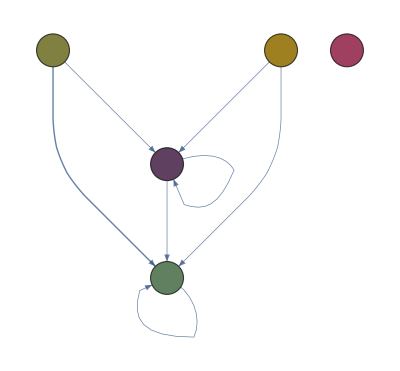

```mathematica
IGEdgeMap[AbsoluteThickness[.5 #]&,EdgeStyle->IGEdgeProp[EdgeWeight],gLungFibMid]
```

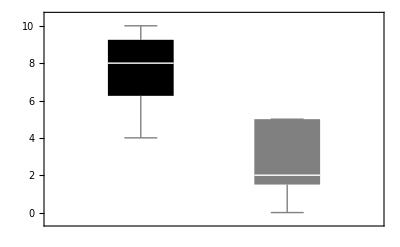

```mathematica
BoxWhiskerChart[{VertexDegree[gLungFib],VertexDegree[gLungFibMid]},ChartStyle->{Black,Gray}]
```

```mathematica
enrGenesMacsGenArcs=Import["/Volumes/ahg_regevdata/users/madler/Postdoc/heterogeneous_communication/GenArcsMonoMacsGenes_continuous_significant.csv"];
```

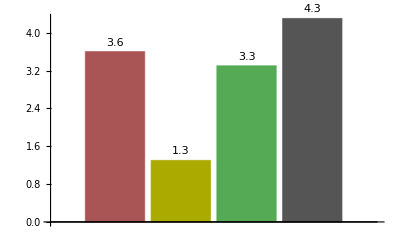

```mathematica
BarChart[Table[N@Round[100(Length@Intersection[Union[ligRecPairs[[;;,1]]],Select[enrGenesMacsGenArcs,#[[1]]==i&][[;;,2]]])/(Length@Select[enrGenesMacsGenArcs,#[[1]]==i&]),.1],{i,1,4}],ChartStyle->Blend/@Subsets[{Yellow,Red,Blue,Green},{3}],LabelingFunction->Above]
```

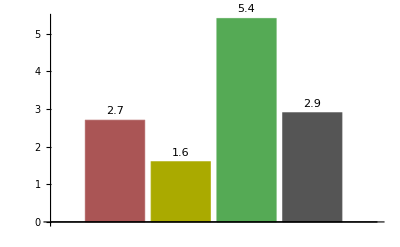

```mathematica
BarChart[Table[N@Round[100(Length@Intersection[Union[ligRecPairs[[;;,2]]],Select[enrGenesMacsGenArcs,#[[1]]==i&][[;;,2]]])/(Length@Select[enrGenesMacsGenArcs,#[[1]]==i&]),.1],{i,1,4}],ChartStyle->Blend/@Subsets[{Yellow,Red,Blue,Green},{3}],LabelingFunction->Above]
```

```mathematica
ligEnrControl=Select[ligMonoMacsControl,Position[enrGenesMacsGenArcs,#]≠{}&];
```

```mathematica
ligEnrControl2=SortBy[(enrGenesMacsGenArcs[[#,;;4]]&/@Position[enrGenesMacsGenArcs,#][[;;,1]]&/@ligEnrControl)[[;;,1]],-#[[4]]&][[;;,;;2]];
```

```mathematica
recEnrControl=Select[recMonoMacsControl,Position[enrGenesMacsGenArcs,#]≠{}&];
```

```mathematica
recEnrControl2=SortBy[(enrGenesMacsGenArcs[[#,;;4]]&/@Position[enrGenesMacsGenArcs,#][[;;,1]]&/@recEnrControl)[[;;,1]],-#[[4]]&][[;;,;;2]];
```

```mathematica
ligRecEnrControl=Select[ligRecPairsMonoMacsControl,Length[DeleteCases[Position[enrGenesMacsGenArcs,#]&/@#,{}]]>1&];
```

```mathematica
ligRecEnrControl2=SortBy[{SortBy[#,-#[[4]]&][[1,;;2]]&/@(enrGenesMacsGenArcs[[#,;;4]]&/@Position[enrGenesMacsGenArcs,#][[;;,1]]&/@ligRecEnrControl[[;;,1]]),SortBy[#,-#[[4]]&][[1,;;2]]&/@(enrGenesMacsGenArcs[[#,;;4]]&/@Position[enrGenesMacsGenArcs,#][[;;,1]]&/@ligRecEnrControl[[;;,2]])}ᵀ,#[[;;,1]]&];
```

```mathematica
gLungMacMid=Graph[Range@4,DirectedEdge@@@(#[[1]]&/@Tally[ligRecEnrControl2[[;;,;;,1]]]),EdgeWeight->Thread[DirectedEdge@@@(#[[1]]&/@Tally[ligRecEnrControl2[[;;,;;,1]]])->Tally[ligRecEnrControl2[[;;,;;,1]]][[;;,2]]],VertexStyle->Thread[Range@4->Blend/@Subsets[{Yellow,Red,Blue,Green},{3}]],VertexSize->0.5];
```

```mathematica
IGEdgeMap[AbsoluteThickness[.5 #]&,EdgeStyle->IGEdgeProp[EdgeWeight],gLungMacMid]
```

-Graphics-

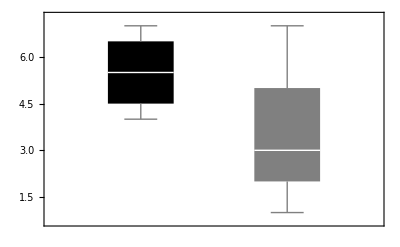

```mathematica
BoxWhiskerChart[{VertexDegree[gLungMac],VertexDegree[gLungMacMid]},ChartStyle->{Black,Gray}]
```